## Prerequisite

## Package & Initial Declaration

```mathematica
(* the package KiHA needs to be loaded for the function dot[_,_] *)
Needs["KiHA`","/Users/tianhengwang/Documents/GitHub/ClassicalSpinOneLoop/kinematicHopfAlgebra-main/KiHA.wl"]
```

KiHA(v2.0),Copyright 2022,author Gang Chen. It is licensed under the GNU General Public License v3.0.
 KiHA is based on the work of Kinematic Hopf Algebra in CTP of Queen Mary University of London.
 It generates the duality all-n numerator for colour-kinematic duality and double copy in heavy mass effective 
 theory(HEFT), Yang-Mills/Gravity theory and Yang-Mills-Scalar/Gravity-Scalar. 
 KiHA is built on some basic functions written by Gustav Mogull and Gregor Kaelin.
 use ?KiHA`* for help and a series of papers (2111.15649, 2208.05519, 2208.05886) for more reference.

```mathematica
Unprotect[p,F,ϵ,v,W];
declareVectorHead[{p,q,P,l,k,ϵ,v,w,a,at,b}]
declareTensorHead[{F,H,W,V,S},{"rank"-> 2}]
declareAntiTensorHead[{F,H,S}]
Protect[p,F,ϵ,v,W];
```

p declared as a 4-dimensional vector header.

q declared as a 4-dimensional vector header.

P declared as a 4-dimensional vector header.

l declared as a 4-dimensional vector header.

k declared as a 4-dimensional vector header.

ϵ declared as a 4-dimensional vector header.

v declared as a 4-dimensional vector header.

w declared as a 4-dimensional vector header.

a declared as a 4-dimensional vector header.

at declared as a 4-dimensional vector header.

b declared as a 4-dimensional vector header.

F declared as a 4-dimensional rank-2 tensor header.

H declared as a 4-dimensional rank-2 tensor header.

W declared as a 4-dimensional rank-2 tensor header.

V declared as a 4-dimensional rank-2 tensor header.

S declared as a 4-dimensional rank-2 tensor header.

```mathematica
SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

## Useful Function Modules and Replacement Rules

```mathematica
ClearAll[FTtransfer]
FTtransfer[f_]:=Module[{logft,ftres},logft=((Series[f,{eps,0,1}]//Normal)//Cases[#,Times[gf__,Log[t]]:>Times[gf,Assuming[ω>0,Sqrt[2π]FourierTransform[  Log[Abs[t]],t,ω]//Simplify]]]&)[[1]];
ftres=logft/. {a_ t^od_:> (-I)^od D[a,{ω,od}], a_ t:> -I D[a,ω]}/.ω->1] (* the function computes the t Fourier integral *)
```

```mathematica
(* The module below computes the series expansion of the elliptic integrals in powers of y4. The elliptic integrals in question only appear in the Y-diagram contributions. *)
ClearAll[integralQ,notyt4Q,intD] 
integralQ[f_]:= If[Head[f]===Inactive[Integrate],True,False]
notyt4Q[f_]:=If[Cases[f,y4,All]==={},True,False]
intD[f_integrate,yt4_,od_]:=intD[f,yt4,od]=Module[{intvar=f[[2,1]],ra=f[[2,2]],rb=f[[2,3]],int=f[[1]]},(Sum[Binomial[od,od1]D[D[int,{intvar,od-1-od1}],{yt4,od1}],{od1,0,od-1}])/.intvar->0/.yt4->0//Expand]
(*intD[a_notyt4Q f_,yt4_,od_]:=a intD[ f,yt4,od]*)
intD[a__ f_integrate,yt4_,od_]:=intD[a f,yt4,od]=Sum[Binomial[od,od1] D[Times[a],{yt4,od-od1}] intD[ f,yt4,od1],{od1,1,od}] /.yt4->0//Expand
intD[f_integrate,yt4_,0]:=0
intD[f_,yt4_,od_]:=D[f,{yt4,od}]/.yt4->0
(* The od1=0 case is not needed as the series expansion always vanishes at yt4=0 *)
ClearAll[intSeries]
intSeries[f_,{var_,od_}]:=Sum[intD[f,var,odi] var^odi/(odi!)//FunctionExpand//Expand,{odi,0,od}]
intSeries[f_Plus,{var_,od_}]:=Sum[Sum[intD[f[[jj]],var,odi] var^odi/(odi!),{odi,0,od}],{jj,Length@f}]
```

```mathematica
(* The functions below replace the relevant variables present in the expression for the eikonal with their respective values. *)
ClearAll[Y2,Y4]
Y2[reps_]:=Y2[reps]=dot[a,a]/(-dot[b,b])/.reps
Y4[reps_]:=Y4[reps]=dot[a,b]/(-dot[b,b])/.reps
repAt2A={at[1]->I a[1]};
repTs={T[f1_,repab_]:>T[f1/.y2->(Y2[repab])/.y4->(Y4[repab])/.dot[b,b]->(dot[b,b]/.repab)]};
```

```mathematica
numValuesExact={dot[b[0],b[0]]->-1,dot[a[1],b[0]]->-1/5,y->12/10,ξ->1/2,dot[a[1],a[1]] ->-1/5,eps[a[1],b[0],v[1],v[2]]->√(-1+y^2) √(-dot[a[1],a[1]]-dot[a[1],b[0]]^2),C[2]->1,m[i_]:>1};
repEps=eps[a[1],b[0],v[1],v[2]]->√(-1+y^2) √(-dot[a[1],a[1]]-dot[a[1],b[0]]^2);
repEpsAt=eps[at[1],b[0],v[1],v[2]]->I √(-1+y^2) √(-dot[a[1],a[1]]-dot[a[1],b[0]]^2);
```

## Data

The data provided here are to be dressed with the overall factor in the section Global Constants. The integration constant is also defined in the same section.

All the expressions are provided for the test-body/probe-limit sector where m[2]>>m[1]. The opposite probe-limit sector can be obtained by swapping the relevant variables.

## Global Constants

```mathematica
overallConstant=-(16Gn π)^2/(4m[1] m[2])1/m[2];
```

```mathematica
integrationConstant={ C[2]->-1/(64 π^2)};
```

## Closed-Form Expression for the Aligned-Spin Eikonal Phase

```mathematica
EikonalClosedFormList="data";
```

## Spin Expansion of the Eikonal Phase at y=2 and b[0].b[0]=-1 up to O(a^8)

```mathematica
EikonalSpinExpansion="data";
```

## Eikonal for a Test Kerr Black Hole in the Spinless Background

```mathematica
intScalarSpin="data";
```

## Examples

We illustrate with examples how to manipulate the expressions provided in this notebook in several use cases.

## Analytic Spin Expansion

### Replacement Rules for the Elliptic Integrals

Here we generate the rules to replace the elliptic integrals (given in the form of the placeholder function integrate[...]) with Mathematica’s built-in elliptic functions.

```mathematica
ellipticInt=EikonalClosedFormList//Cases[#,integrate[__],All]&//Union
```

{integrate[1/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),{K[1],0,y4}],integrate[K[1]/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),{K[1],0,y4}]}

```mathematica
ef1=Integrate[1/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),K[1]];
ef2=Integrate[K[1]/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),K[1]];
```

```mathematica
repEllipticIntegrals={Rule[ellipticInt[[1]],(ef1/.K[1]->y4//Simplify)-(ef1/.K[1]->0//Simplify)],Rule[ellipticInt[[2]],(ef2/.K[1]->y4//Simplify)-(ef2/.K[1]->0//Simplify)]};
```

#### Numerical Checks for the Incomplete Elliptic Integrals

```mathematica
ellipticInt
```

{integrate[1/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),{K[1],0,y4}],integrate[K[1]/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1])),{K[1],0,y4}]}

```mathematica
ta=ellipticInt[[1]]//intSeries[#,{y4,36}]&;
ta/.y4->-2/10/.y2->-5/6//N[#,50]&
```

0.19761584050847514393182274788191169963315162414802

```mathematica
ellipticInt[[1]]/.repEllipticIntegrals/.y4->-2/10/.y2->-5/6//N[#,50]&
```

0.19761584050849003019680163460166772261549028135373

```mathematica
NIntegrate[1/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1]))/.y4->-2/10/.y2->-5/6,{K[1],0,-2/10}, WorkingPrecision->50]
```

0.19761584050849003019680163460166772261549028135373

```mathematica
ta=ellipticInt[[2]]//intSeries[#,{y4,36}]&;
```

```mathematica
ta/.y4->-2/10/.y2->-5/6//N[#,50]&
```

-0.021128746506134010040545837477768143121459128423558

```mathematica
ellipticInt[[2]]/.repEllipticIntegrals/.y4->-2/10/.y2->-5/6//N[#,50]&
```

-0.02112874650613383400629549602790203621217626898094+0. ⅈ

```mathematica
NIntegrate[K[1]/(√(y2+2 y4-2 K[1]) √(y2+2 y4+(-2+K[1]) K[1]))/.y4->-2/10/.y2->-5/6,{K[1],0,-2/10},Method->"LocalAdaptive", WorkingPrecision->50]
```

-0.02112874650613383400629549602790203621217626898094

### Spin Expansion Involving the Elliptic Integrals

```mathematica
(* The module below deals with the double expansion in y4 and y2 of the elliptic integrals *)
repEK={EllipticE[f_]:>elip[2,f],EllipticK[f_]:>elip[1,f]};
repEKback={elip[2,f_]:>EllipticE[f],elip[1,f_]:>EllipticK[f]};
repElliptic={Rule[ellipticInt[[1]],intSeries[ellipticInt[[1]],{y4,10}]],Rule[ellipticInt[[2]],intSeries[ellipticInt[[2]],{y4,10}]]};
ClearAll[expandinys]
expandinys[f_]:=Module[{tc},tc= f/.repElliptic/.repEK//Collect[#,elip[__],Simplify]&;tc=(Series[tc/.repEKback,{y4,0,10},{y2,0,5}]//Normal)]
```

We use the following example to illustrate the procedure for computing the spin expansion of a given term in the eikonal phase that involves the elliptic integrals

```mathematica
mm=9;
Length@EikonalClosedFormList[[mm]]

(* Expand the elliptic integrals in y4 and y2 first *)
ClearAll[foo]
Monitor[foo=Sum[EikonalClosedFormList[[mm]][[jj]]/.T[f1_,f2_]:>T[expandinys[f1],f2]/.repTs,{jj,Length@EikonalClosedFormList[[mm]]}],jj];
foo=foo/.T[f_]:>f;
```

8

```mathematica
Length@foo
(* Replace all the dynamical variables with their actual values and compute their expansion in spin *)
(* For mere illustrative purposes, we choose dot[b[0],b[0]]-> -1 here *)
Monitor[expansion=Sum[Series[foo[[ii]]/.repAt2A /.dot[b[0],b[0]]->-1/.a[1]->z a[1],{z,0,10}]//Normal,{ii,Length@foo}],ii];
expansion=expansion//Collect[#,z,Simplify]&;

(* Integrate out the remaning σ[i] integrals *)
expansion=Integrate[Integrate[Integrate[Integrate[expansion,{σ[1],0,1}],{σ[2],0,1}],{σ[3],0,1}],{σ[4],0,1}]//Collect[#,z,Simplify]&;
```

68

```mathematica
expansion
```

(3 π y z C[2] eps[a[1],b[0],v[1],v[2]] m[1]^2 m[2]^4)/(4 √(-1+y^2))-(3 π y z^3 C[2] (2 (4+9 ξ^2) dot[a[1],a[1]]+5 (8+15 ξ^2) dot[a[1],b[0]]^2) eps[a[1],b[0],v[1],v[2]] m[1]^2 m[2]^4)/(64 √(-1+y^2))+1/(512 √(-1+y^2))3 π y z^5 C[2] (16 (3+20 ξ^2+10 ξ^4) dot[a[1],a[1]]^2+28 (24+155 ξ^2+70 ξ^4) dot[a[1],a[1]] dot[a[1],b[0]]^2+63 (16+100 ξ^2+45 ξ^4) dot[a[1],b[0]]^4) eps[a[1],b[0],v[1],v[2]] m[1]^2 m[2]^4-1/(8192 √(-1+y^2))3 π y z^7 C[2] (16 (40+546 ξ^2+840 ξ^4+175 ξ^6) dot[a[1],a[1]]^3+72 (240+3234 ξ^2+4900 ξ^4+945 ξ^6) dot[a[1],a[1]]^2 dot[a[1],b[0]]^2+66 (960+12768 ξ^2+19180 ξ^4+3675 ξ^6) dot[a[1],a[1]] dot[a[1],b[0]]^4+429 (128+1680 ξ^2+2520 ξ^4+483 ξ^6) dot[a[1],b[0]]^6) eps[a[1],b[0],v[1],v[2]] m[1]^2 m[2]^4+1/(131072 √(-1+y^2))3 π y z^9 C[2] (256 (35+810 ξ^2+2583 ξ^4+1680 ξ^6+189 ξ^8) dot[a[1],a[1]]^4+1408 (280+6435 ξ^2+20412 ξ^4+13125 ξ^6+1386 ξ^8) dot[a[1],a[1]]^3 dot[a[1],b[0]]^2+4576 (560+12780 ξ^2+40383 ξ^4+25830 ξ^6+2709 ξ^8) dot[a[1],a[1]]^2 dot[a[1],b[0]]^4+5720 (896+20304 ξ^2+64008 ξ^4+40887 ξ^6+4284 ξ^8) dot[a[1],a[1]] dot[a[1],b[0]]^6+12155 (256+5760 ξ^2+18144 ξ^4+11592 ξ^6+1215 ξ^8) dot[a[1],b[0]]^8) eps[a[1],b[0],v[1],v[2]] m[1]^2 m[2]^4

## Numerical Evaluation of Finite Spin Effects

We consider one term in the eikonal and compare between its direct numerical evaluation and the numerical evaluation of its spin expansion.

```mathematica
numValuesFixed={dot[b[0],b[0]]->-1,y->12/10,C[2]->1,ξ->1/2,m[i_]:>1}; (* These values can be altered to one's own choice within their physical ranges; -1 < costheta < +1, 0 < na < 1. *)
numValuesVar={dot[a[1],b[0]]-> - na costheta,dot[a[1],a[1]]->-na^2};
```

We consider the same term as before:

```mathematica
mm=9;
foo=EikonalClosedFormList[[mm]]//Simplify;
Length@foo
Head[foo]
Monitor[foo=Table[foo[[jj]]/.repEllipticIntegrals/.repTs,{jj,Length@foo}],jj];
```

8

Plus

```mathematica
example=foo/.T[f_]:>f/.repAt2A/.repEps/.numValuesFixed/.numValuesVar//Total;
```

```mathematica
exampleWithChosenValues=example/.{na->20/30,costheta->10/13};
```

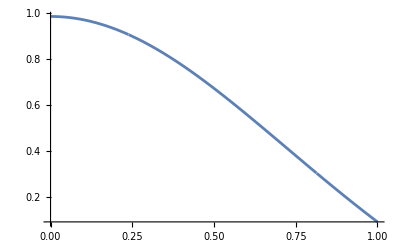

```mathematica
Plot[exampleWithChosenValues,{σ[1],0,1},PlotRange->All]
```

Recall the aforementioned analytic spin expansion

```mathematica
expansionNum=expansion/.z->1/.repAt2A/.repEps/.numValuesFixed/.numValuesVar;
```

```mathematica
Monitor[exampleNum4Plot=Table[tmp=example/.{costheta->12/13,na->jj/30};
tmpIntegrated=NIntegrate[tmp,{σ[1],0,1},WorkingPrecision->20],{jj,1,20}],{jj}];
```

```mathematica
Monitor[expansionNum4Plot=Table[expansionNum/.{costheta->12/13,na->jj/30}//N,{jj,1,20}],{jj}];
```

```mathematica
finiteSpin=Table[toPlot[jj/30.,exampleNum4Plot[[jj]]],{jj,1,20}]//Flatten;
finiteSpin=finiteSpin/.toPlot[f__]:>{f};
spinExpansion=Table[toPlot[jj/30.,expansionNum4Plot[[jj]]],{jj,1,20}]//Flatten;
spinExpansion=spinExpansion/.toPlot[f__]:>{f};
```

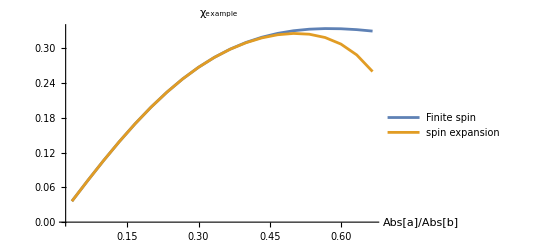

```mathematica
ListLinePlot[{finiteSpin,spinExpansion},AxesLabel->{Abs[a]/Abs[b]},PlotRange->Full,PlotLabel->"χ_example",PlotLegends->{"Finite spin","spin expansion"}]
```

## Result of eikonal for a background scalar scattering with a test Kerr black hole

```mathematica
intScalarSpinNum=intScalarSpin/.repAt2A/.repEps/.numValuesFixed/.numValuesVar/.t[i_]:>σ[i];
```

```mathematica
NIntegrate[intScalarSpinNum/.{costheta->2/10,na->19/20}//Total,{σ[1],0,1},{σ[2],0,1},WorkingPrecision->10]
```

139.5967042

```mathematica
(* The evaluation module below takes some time to run *)
```

```mathematica
foo1=intScalarSpinNum//Total;
Monitor[eikonalScalarSpinNum=Table[foo2=foo1/.{costheta->ii/10,na->jj/20};
tmpNum=NIntegrate[foo2,{σ[1],0,1},{σ[2],0,1},WorkingPrecision->15],{ii,1,9},{jj,1,15}],{ii,jj}];
```

```mathematica
SaveToCell[eikonalScalarSpinNum]
```

```mathematica
eikonalScalarSpinNum="data";
```

```mathematica
eikonalScalarSpinNum[[1,1]]
```

23.469462866437

```mathematica
(overallConstant C[2]/.integrationConstant/.Gn->1/.m[i_]:>1)
```

1

```mathematica
eikonalScalarSpinNum2Plot=Table[toPlot[jj/20.,ii/10.,(overallConstant C[2]/.integrationConstant/.Gn->1/.m[i_]:>1)eikonalScalarSpinNum[[ii,jj]]],{ii,1,9},{jj,1,15}]//Flatten;
eikonalScalarSpinNum2Plot=eikonalScalarSpinNum2Plot/.toPlot[f__]:>{f};
```

```mathematica
eikonalScalarSpinNum2Plot[[1]]
```

{0.05,0.1,23.469462866437}

```mathematica
ListPlot3D[eikonalScalarSpinNum2Plot,AxesLabel->{Abs[a]/Abs[b],Cos[θ]},PlotRange->Full,PlotLabel->"χ"]
```

-Graphics3D-

## aligned spin a.b=0

```mathematica
ClearAll[leadingSeries,LdTerm]
leadingSeries[expr_,{x_,x0_}]:=Normal[expr/.x->Series[x,{x,x0,1}]/.Verbatim[SeriesData][a__,{b_,___},c__]:>SeriesData[a,{b},c]]
LdTerm[f_,var_]:=leadingSeries[f,{var,∞}]//Normal
```

```mathematica
intScalarSpinOriginal=intScalarSpin/.Piecewise[{{f1_,r1_},{f2_,r2_}},0]:>f2/.t[i_]:>σ[i];
```

```mathematica
numvaluesFixb={y->6/5,C[2]->1,m[i_]:>1,dot[a[1],a[1]]->-1,dot[a[1],b[0]]-> - nb costheta,dot[b[0],b[0]]->- nb^2};
```

```mathematica
fnum2=intScalarSpinOriginal/.numvaluesFixb;
```

```mathematica
Monitor[leadingAlign=Table[leadingSeries[fnum2[[ii]],{costheta,0}]//Simplify,{ii,Length@fnum2}]//Total;,ii]
```

```mathematica
Monitor[numresAlign=Table[fnumall2=leadingAlign/.{nb->jj/100};
numres=NIntegrate[fnumall2,{σ[1],0,1},{σ[2],0,1},WorkingPrecision->10],{jj,101,120}];,{jj}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
numresAlign
```

{13324.78817,4792.747953,2657.983859,1756.432368,1282.830717,993.5102453,801.973961,667.2563974,569.1305031,497.4653759,437.0672626,389.4381868,351.2473513,318.7389025,292.470524,269.3045772,249.3856581,232.617108,217.5562963,204.3338535}

```mathematica
numresAlignxy=Table[T[(100+jj)/100.,Log[numresAlign[[jj]]]],{jj,1,Length@numresAlign}]//Flatten;
numresAlignxy=numresAlignxy/.T[f__]:>{f};
```

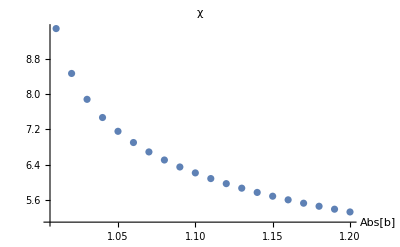

```mathematica
ListPlot[numresAlignxy,AxesLabel->{Abs[b]},PlotRange->Full,PlotLabel->"χ"]
```

```mathematica
ftest=(dot[b[0],b[0]]-dot[a[1],a[1]])^(-3/2)/.numvaluesFixb;
Monitor[testnum=Table[fnumall2=ftest/.{nb->jj/100},{jj,101,120}];,{jj}]
testnum4=Table[T[(100+jj)/100.,Log[39.2*Im[testnum[[jj]]]]//N],{jj,1,Length@testnum}]//Flatten;
testnum4=testnum4/.T[f__]:>{f};
```

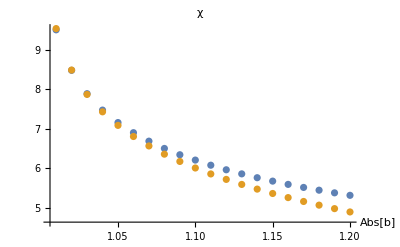

```mathematica
ListPlot[{numresAlignxy,testnum4},AxesLabel->{Abs[b]},PlotRange->Full,PlotLabel->"χ"]
```

```mathematica
numresAlignxy
```

{{1.01,9.497381352},{1.02,8.474859211},{1.03,7.885323167},{1.04,7.471039967},{1.05,7.156824413},{1.06,6.901244374},{1.07,6.68707614},{1.08,6.503174376},{1.09,6.344109763},{1.1,6.209525958},{1.11,6.080087102},{1.12,5.964705154},{1.13,5.86149068},{1.14,5.76437228},{1.15,5.678363889},{1.16,5.595842996},{1.17,5.519000526},{1.18,5.449393789},{1.19,5.382457651},{1.2,5.319755193}}